```mathematica
(*Initialize 1-loop determinant*)
Γq[x_+0]:=Γ0q[x]
Γq[w_(x_+y_)]:=Γq[w x+w y]
Γq[x_+k_Integer?Positive]:=qNum[x+k-1] Γq[x+k-1]
Γq[x_+k_Integer?Negative]:= Γq[x+k+1]/qNum[x+k]
Gq[x_+0]:=G0q[x]
Gq[w_(x_+y_)]:=Gq[w x+w y]
Gq[x_+k_Integer?Positive]:=Γq[x+k-1] Gq[x+k-1]
Gq[x_+k_Integer?Negative]:= Gq[x+k+1]/Γq[x+k]
qNum[u_]:=(1-q^u)/(1-q)
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Sum[
(fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]])^2/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
```

(q (1+q^(4 σ)))/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2),(1-q)^(-2 σ^2) (-1+q)^(-2 σ^2)
```

```mathematica
BII[σ_,t_]=1+ϵ t((q (1+q^(4 σ)))/((-1+q)^2 (-1+q^(2 σ))^2))+ϵ^2 t^2((q^2 ((q-q^(2 σ))^2+q^(4+8 σ) (q-q^(2 σ))^2+q^(2+4 σ) (1+q)^2 (-1+q^(2 σ))^2+q^4 (-1+q^(1+2 σ))^2+q^(8 σ) (-1+q^(1+2 σ))^2))/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2));
CII[σ_]=(1-q)^(-2 σ^2) (-1+q)^(-2 σ^2)1/(Gq[1+2σ]Gq[1-2σ]);
τII[σ_,shift_,t_]:=Sum[s^n ξ^(2n+2shift)ϵ^(n^2+2shift n)t^((σ+shift+n)^2)CII[σ+shift+n]BII[σ+shift+n,t],{n,-2,2}]
nNorm = 1/CII[σ];
```

```mathematica
τII1=nNorm τII[σ,0,t]+O[ϵ]^3;
τII2=s^(1/2)nNorm τII[σ,1/2, t]+O[ϵ]^3;
```

```mathematica
(γ1-γ2 t ϵ)  /.{β1->-1,β2->0,γ1->0,γ2->-t^(-1/2)}
```

√t ϵ

```mathematica
(*eqn 1 is: τ1^2-( 1- q^(-2 θt) t )uτ1 dτ1 -(1-q)t^(1/2)τ2 τ3 == 0 *)
nϵ = 1; nξ=2;
a=(Coefficient[Coefficient[τII1^2,ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
b=(Coefficient[Coefficient[ -(τII1/.t-> q^-1 t)(τII1/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
c=(Coefficient[Coefficient[ (γ1-γ2 t ϵ)  (τII2/.t-> q^-1 t)(τII2/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
(a+ b+c /.{β1->-1,β2->0,γ1->0,γ2->-t^(-1/2)}//PowerExpand//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify
```

0

```mathematica
nϵ = 2; nξ=0;
a=(Coefficient[Coefficient[τII1^2,ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
b=(Coefficient[Coefficient[ -(τII1/.t-> q^-1 t)(τII1/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
c=(Coefficient[Coefficient[ (γ1-γ2 t ϵ)  (τII2/.t-> q^-1 t)(τII2/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
(a+ b+c /.{β1->-1,β2->0,γ1->0,γ2->-s t^(-1/2)}//PowerExpand//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify
```

-1/((q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)((1-q)^(4 σ^2)-ⅇ^(4 ⅈ π σ^2) (-1+q)^(4 σ^2)) (1-q)^(-2-4 σ^2) (q^2+q^4+q^(4 σ)+q^(8 σ)-2 q^(1+2 σ)-2 q^(5+2 σ)+2 q^(2+4 σ)+2 q^(4+4 σ)+q^(6+4 σ)-8 q^(3+6 σ)+2 q^(2+8 σ)+2 q^(4+8 σ)+q^(6+8 σ)-2 q^(1+10 σ)-2 q^(5+10 σ)+q^(2+12 σ)+q^(4+12 σ)) t^(2+2 σ^2)

```mathematica
c//Simplify
```

(2 q^(1/4+2 σ+σ^2) t^(3/2) ((q^(7/2) γ1)/((-1+q)^2 (q-q^(2 σ))^2)+(q^(3/2+4 σ) γ1)/((-1+q)^2 (q-q^(2 σ))^2)+(q^(3/2) γ1)/((-1+q)^2 (-1+q^(1+2 σ))^2)+(q^(7/2+4 σ) γ1)/((-1+q)^2 (-1+q^(1+2 σ))^2)-γ2))/((-1+q^(2 σ))^2)

```mathematica
τII1^2-(τII1/.t-> q^-1 t)(τII1/.t-> q^1 t)//Simplify
Coefficient[%,ξ,0]//Simplify
```

1/(-1+q)^4 t (-(q^(-1-2 σ) (q-q^(2 σ))^2 t^(-6 σ) (-(-1+q)^2 t)^(4 σ) G0q[-2 σ] G0q[2 σ] Γ0q[-2 σ] Γ0q[2 σ])/(ξ^2 G0q[2-2 σ] G0q[2 (-1+σ)] Γ0q[2-2 σ] Γ0q[2 (-1+σ)])+(-(-1+q)^2)^(-4 σ) (-((-1+q)^4 ((-(-1+q)^2)^(4 σ)+(-(-1+q)^2 q)^(4 σ)))/((-1+q^(2 σ))^2)-(q^(-1-2 σ) (-1+q^(1+2 σ))^2 t^(2 σ) ξ^2 G0q[-2 σ] G0q[2 σ] Γ0q[-2 σ] Γ0q[2 σ])/(G0q[-2 (1+σ)] G0q[2 (1+σ)] Γ0q[-2 (1+σ)] Γ0q[2 (1+σ)]))) ϵ+O[ϵ]^2

-((1+q^(4 σ)) t ϵ)/((-1+q^(2 σ))^2)

```mathematica
Coefficient[(τII2/.t-> q^-1 t)(τII2/.t-> q^1 t),ξ,0]/.{ϵ->0}/.{G0q:>Gq,Γ0q:>Γq}//Simplify
```

((1+q^(4 σ)) √t)/((-1+q^(2 σ))^2)

```mathematica
Solve[(2+(2 q^(2 σ) √t γ1)/((-1+q^(2 σ))^2))==0,γ1]//Simplify
```

{{γ1→ConditionalExpression[-(q^(-2 σ) (-1+q^(2 σ))^2)/(√t), q≠1]}}

```mathematica
(γ1-γ2 t ϵ)/.{γ1->s^-1 √t,γ2->0}
```

(√t)/s

```mathematica
(*eqn 1 is: τ1^2-( 1- q^(-2 θt) t )uτ1 dτ1 -(1-q)t^(1/2)τ2 τ3 == 0 *)
nϵ = 0; nξ=0;
a=(Coefficient[Coefficient[τII2^2,ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
b=(Coefficient[Coefficient[ -(τII2/.t-> q^-1 t)(τII2/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
c=(Coefficient[Coefficient[ (γ1-γ2 t ϵ)  (τII1/.t-> q^-1 t)(τII1/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
(a+ b+c /.{γ1->s^-1 √t,γ2->0}//PowerExpand//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify
```

0

```mathematica
Solve[(ⅇ^(4 ⅈ π σ) (-1+q)^(4 σ) √t-(1-q)^(4 σ) γ1)==0,γ1]
```

```mathematica
{{γ1->ⅇ^(4 ⅈ π σ) (1-q)^(-4 σ) (-1+q)^(4 σ) √t}}
```

```mathematica
ⅇ^(4 ⅈ π σ) (1-q)^(-4 σ) (-1+q)^(4 σ) /.{σ->.4}//PowerExpand
```

((0.309017-0.951057 ⅈ) (-1+q)^1.6)/(1-q)^1.6

```mathematica
Simplify[Abs[ⅇ^(4 ⅈ π σ) (1-q)^(-4 σ) (-1+q)^(4 σ) ],σ>0]//Simplify
```

ⅇ^(4 σ (-Re[Log[1-q]]+Re[Log[-1+q]]))

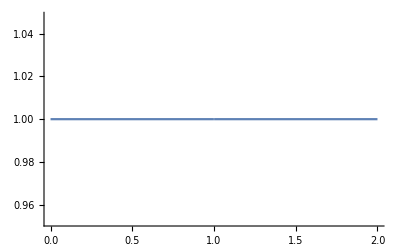

```mathematica
Plot[Abs[((0.30901699437494723-0.9510565162951536 ⅈ) (-1+q)^1.6)/(1-q)^1.6],{q,0,2}]
```

```mathematica
(*eqn 1 is: τ1^2-( 1- q^(-2 θt) t )uτ1 dτ1 -(1-q)t^(1/2)τ2 τ3 == 0 *)
nϵ = 0; nξ=0;
a=(Coefficient[Coefficient[τII2^2,ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
b=(Coefficient[Coefficient[ (-1+t ϵ)(τII2/.t-> q^-1 t)(τII2/.t-> q^1 t),ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
c=(Coefficient[Coefficient[ (γ1+γ2  ϵ)  τII1^2,ϵ,nϵ ],ξ,nξ]//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify;
(a+ b+c /.{γ1->(√t)/s,γ2->0}//PowerExpand//Simplify)/.{G0q:>Gq,Γ0q:>Γq}//Simplify
```

0

```mathematica
Solve[(1+q^(2 σ))^2 √t+(-1+q^(2 σ))^2 s γ1==0,γ1]//Simplify
```

{{γ1→-((1+q^(2 σ))^2 √t)/((-1+q^(2 σ))^2 s)}}

```mathematica
-(2 q (1+q^(2 σ))^2 t^(3/2))/((-1+q)^2 (-1+q^(2 σ))^4)-(2 q^(1+4 σ) (1+q^(2 σ))^2 t^(3/2))/((-1+q)^2 (-1+q^(2 σ))^4)+(4 q^(1+2 σ) (q^2+q^(4 σ)-q^(1+2 σ)-q^(3+2 σ)+q^(4+4 σ)-q^(1+6 σ)-q^(3+6 σ)+q^(2+8 σ)) t^(3/2))/((-1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)+((q^2+q^4+q^(4 σ)+q^(8 σ)-2 q^(1+2 σ)-2 q^(5+2 σ)+2 q^(2+4 σ)+2 q^(4+4 σ)+q^(6+4 σ)-8 q^(3+6 σ)+2 q^(2+8 σ)+2 q^(4+8 σ)+q^(6+8 σ)-2 q^(1+10 σ)-2 q^(5+10 σ)+q^(2+12 σ)+q^(4+12 σ)) t^(3/2))/((-1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)//FullSimplify
```

1/((q-q^(2 σ))^2 (-1+q^(2 σ))^4 (-1+q^(1+2 σ))^2)(q^2+q^(2+16 σ)-2 q^(1+2 σ) (1+q+q^2)-2 q^(1+14 σ) (1+q+q^2)+2 q^(8 σ) (1+(-5+q) q) (1+q+q^2)-2 q^(6 σ) (1+q (3+q (-3+q (3+q))))-2 q^(10 σ) (1+q (3+q (-3+q (3+q))))+q^(4 σ) (1+q (4+q (14+q (4+q))))+q^(12 σ) (1+q (4+q (14+q (4+q))))) t^(3/2)